## Testing HW 3

### code needed -- execute this cell

#### code - find correct function names - general

```mathematica
(* find function names existing in kernel which matches the given pattern *)findPossibleName[functionName_,pattern_] := Module[{possibleNames,distances ,bestMatch ,x},
possibleNames= Names[pattern];
distances = Table[{item, EditDistance[item, functionName]},{item, possibleNames}];
bestMatch=possibleNames[[Flatten[Position[x=Table[Part[item,2], {item, distances}];x, Min[x] ]]]];
If [Length[bestMatch] < 1
, Return[]];
Return[bestMatch[[1]]]
]
```

```mathematica
(* replace first letter and each capital letter by an asterix *)
nameToPattern[funName_] :=StringReplace[StringReplacePart[funName, "*", {1,1}], CharacterRange["A", "Z"] -> "*"]
```

```mathematica
(* find function names existing in kernel which are close to given funcction name; first letter and capital letters are made 'variable' *)
findPossibleName[functionName_] := 
Return[findPossibleName[functionName, nameToPattern[functionName]]];
```

```mathematica
(* find the actual function to call which has a name close to the given name *)
findFunction[functionName_, pattern_, display_] := Module[{useName = functionName, useThis},
If[!NameQ[functionName]
		, Print[Style[StringJoin["     ERROR - no function with name ", functionName, " exists"], Red]];
		    useName= findPossibleName[functionName, pattern];
		     If [useName == Null 
		       , If[display
			, Print[Style["            no suitable replacement found to use ", Red]];
			     Print[Style["            evaluation of function ", functionName, " failed completely", Red]];
			];
			Return[];
		];
];
(* execute the function *)
  If [useName == functionName && display
, Print["function ", functionName, " exists and is used "];
Return[{True, useName}];
,  Print[Style[StringJoin["     ATTEMPTING to use ", useName, " for the test"], Blue]];
Return[{False, useName}];
]	
(*Return[{True,useName}]*)
]
```

```mathematica
(* find the actual function to call which has a name close to the given function name *)
findFunction[functionName_,  display_] := 
  findFunction[functionName, nameToPattern[functionName], display]
```

```mathematica
testFunctionExists[funName_, formalLst_, paramLst_,  pattern_]:=Module [
{foundNames, useFunName,(* useThis,*) res, useThisStr},
(* find a suitably close function name to use *)
foundNames=findFunction[funName, pattern, True]; 
 If[ Length[foundNames] == 0,
	Return[ {StringJoin ["Result for "  <> funName <> ": "], Style[" FUNCIONT DOES NOT EXIST",Red]}]
];	
If[! SameQ[funName,foundNames[[2]]],
Return[ {"Result for "  <> funName <> ": ", Style["MISSPELLED name to " <> foundNames[[2]] <> "?",Red]}]
];
 useFunName = foundNames[[2]];

(* create the funcion to see whether it exists ... *)
 useThisStr = StringJoin["useThis [",
			StringRiffle[formalLst, {"", "_, ", "_"}],
			"] := Apply [ Symbol [ \"", useFunName,
			"\"] , ",
			StringRiffle[formalLst, {"{",", ", "}"}],
			" ]"
			];
(*Print[" XXXX"<>useThisStr<>"XXX"];*)
Clear[useThis];
ToExpression[useThisStr]; (* this creates the function as
						if the above string had been typed in *)

(* excute the function and report the result... *)
 res = {"Result for "  <> useFunName <> ": ", paramLst,
Check[ 
TimeConstrained[ Apply [useThis, paramLst], 1, Style["EXECUTION TOOK TOO LONG ", Red]
] , Style[" EXECUTION CAUSED AN EXCEPTION ",Red]
]}
]
```

```mathematica
testFunctionExists[funName_, formalLst_, paramLst_]:=
(* find the actual function to use which has a name close to the given function name *)
testFunctionExists[funName,  formalLst, paramLst, nameToPattern[funName]]
```

#### code - verify return type - general

```mathematica
verifyReturnTypeAndStructure[result_, {correctType_, correctStructure_}] := Module[
{correctTypes, errorMsg},
If [!SameQ[Head[result], correctType],
	errorMsg =Style[StringJoin["Error - incorrect type returned; should be a ", ToString[correctType]], Red];
	Print[errorMsg];
	Return[False]
];
If[correctType === List,
(* check type of each list element in result against correctStructure type *)
If[SameQ[correctStructure[[1]] ,"individual"],
(* types in list might be different *)
correctTypes =Table[SameQ[Head[result[[i]]], Head[correctStructure[[2,i]]]],{i, 1, Length[correctStructure[[2]]]}];
(*Print["correctStructure ", correctStructure, " correctypes " ,correctTypes, " ", Table[Head[result[[i]]],{i, 1, Length[correctStructure[[2]]]}], " ",
Table[Head[correctStructure[[2,i]]],{i, 1, Length[correctStructure[[2]]]}]];*)
If [! Apply[And,correctTypes],
	errorMsg=Style["Error - incorrect types of list elements in result", Red];
	Print[errorMsg];
	Return[False]
 ];,
    (* else - not individual structure 
all elements should have the same structure as the one given *)
 Print["repetitive structures are NOT INCLUDED SO FAR INTO TESTING HARNESS"];
];
Print[Style["Correct types", Blue]];
Return[True];
];
Print[Style["Correct types", Blue]];
Return[True]
]
```

#### RandomWalk checking code: i) verify length of list, ii) x from 0 to length, iii) min and max y coordinates, iv) mod from node to node {1,1} or {1,-1}, or {1,0} v) prob for each type of direction

```mathematica
(* check basis features of the random walk in 2D *)checkRandomWalkResult[resultLst_, {targetLength_, targetMin_, targetMax_}, straightProb_]:=Module [
{distances, talliedDistances, allowedDistances= {{1,1},{1,-1}},
result, probLst = {0.5, 0.5}},
(* check length and range *)
If[!checkRandomWalkLengthRange[resultLst, targetLength],
Return[False]
];
(* are y-values between min and max?*)
If [ Min[resultLst[[All,2]]]< targetMin || Max[resultLst[[All,2]]]> targetMax ,
Print[Style[ "Incorrect y-values: some too large or too small",Red]];
Return[False]
];
(* are differences from one to next of the allowed distances? *)
If[straightProb≠ 0,
AppendTo[allowedDistances, {1,0}];
probLst = {(1-straightProb)/2., (1-straightProb)/2., straightProb};
];
result = tallyDistances[resultLst, allowedDistances, False];
(* if tally shows problems - return *)
If[! result[[1]],
Return[result[[1]]];
];
Return[checkProbabilities[result[[2]],result[[3]],probLst]];
Return[False]
]
```

```mathematica
(* checks whether result lst has the correct length and range (x-values) *)checkRandomWalkLengthRange[resultLst_, targetLength_]:=Module[
{},
(* is length to be checked - and is condition failed? *)
If [targetLength > 0 && Length[resultLst] ≠ targetLength,
Print[Style[StringJoin[ "Incorrect length of result: is ", 
					ToString[Length[resultLst]], " instead of " ,
					ToString[ targetLength]],Red]];
Return[False]
];
(* are x-values from 0 to lenght-1 *)
If [ !SameQ[Range[0,Length[resultLst]-1], resultLst[[All,1]]],
Print[Style[ "Incorrect x-values: not 0, 1, 2, 3, ....."],Red];
Return[False]
];
Return[True]
]
```

```mathematica
(* check basis features of the random walk in 3D *)
checkRandomWalk3DResult[resultLst_, {targetLength_, lower_, upper_}]:=Module [
{distances, talliedDistances, allowedDistances= {{1,1,1},{1,1,-1},{1,-1,1},{1,-1,-1}},
result, probLst = {0.25, 0.25,0.25, 0.25}},
(* is length to be checked - and is condition failed? *)
(* check length and range *)
If[!checkRandomWalkLengthRange[resultLst, targetLength],
Return[False]
];
(* are y- and z-values between lower and upper?*)
If [ Min[resultLst[[All,2]]]< lower[[1]] || Max[resultLst[[All,2]]]> upper[[1]] ||
 Min[resultLst[[All,3]]]< lower[[2]] || Max[resultLst[[All,3]]]> upper[[2]] ,
Print[Style[ "Incorrect y- or z-values: some too large or too small",Red]];
Return[False]
];
(* check probabilities - only make sense for long enough walks *)
result = tallyDistances[resultLst, allowedDistances, False];
(* if tally shows problems - return *)
If[! result[[1]],
Return[result[[1]]];
];
Return[checkProbabilities[result[[2]],result[[3]],probLst]];
]
```

```mathematica
(* determine the probabiliges for each of the allowed distances (order in allowedDistances and 
probs is the same) and return the difference between what it should be and
what it is *)
checkProbabilities[tallyLst_, allowedDistances_, probs_]:= Module[
{sortedTally, total, probComputed},
(*Print[" in checkProb ", tallyLst,  " ", allowedDistances];*)
(* sort tallyLst, so that info is in same order as probabilities*)
sortedTally=SortBy[tallyLst, Position[allowedDistances, #[[1]]][[1,1]]&];
total = Total[sortedTally[[All,2]]];
(*Print["sorted = ", sortedTally, "and total = ", total];*)
(* determine max difference to expected probs *)
probComputed= N[sortedTally[[All,2]]/total];
Return[probComputed];
]
```

```mathematica
(* determine how often each of the allowed distances appears in the resultlstl; if 'straight'
steps are allowe (modWalk), then a straight distance must be added to the allowed distances *)
tallyDistances[resultLst_, allowedDistancesRaw_, straightProb_]:=Module [
{allowedDistances =allowedDistancesRaw , distances, talliedDistances},
(*Print["in tallyDistance"];*)
(* are differences from one to next of the allowed distances? *)
distances=Table[resultLst[[i]]-resultLst[[i-1]],{i, 2, Length[resultLst]}];
talliedDistances =Tally[distances];
(*Print["tallied distances ", talliedDistances, " ", allowedDistances];*)
(* check that only allowed distances occur *)
If [! Apply[And,Table[MemberQ[allowedDistances, item[[1]]], {item, talliedDistances}]],
Print[Style["Some steps are not up or down ",Red]];
Return[{False}]
];
Return[{True, talliedDistances, allowedDistances}]
]
```

```mathematica
testFunction[funName_, formalLst_, multParamLst_,  checkParamLst_]:=Module [
{foundNames, useFunName,(* useThis,*) res, useThisStr, paramLst, resStr, checkRes, pattern},
(* find a suitably close function name to use *)
pattern=nameToPattern[funName];
foundNames=findFunction[funName, pattern, True]; 
 If[ Length[foundNames] == 0,
	Return[ {StringJoin ["Result for "  <> funName <> ": "], Style["function IS MISSING",Red]}]
];
(* is the CORRECT name found? *)
If [!SameQ[funName, foundNames[[2]]],
		Return[ {StringJoin ["Result for "  <> funName <> ": "], 
				Style[StringJoin["MISSPELLED name to  ", foundNames[[2]], "?"],Red]}]
];
 useFunName = foundNames[[2]];

(* create the funcion to see whether it exists ... *)
 useThisStr = StringJoin["useThis [",
			StringRiffle[formalLst, {"", "_, ", "_"}],
			"] := Apply [ Symbol [ \"", useFunName,
			"\"] , ",
			StringRiffle[formalLst, {"{",", ", "}"}],
			" ]"
			];
(*Print[" XXXX"<>useThisStr<>"XXX"];*)
Clear[useThis];
ToExpression[useThisStr]; (* this creates the function as
						if the above string had been typed in *)

(* excute the function and report the result... *)
Table[res = Check[ 
TimeConstrained[ Apply [useThis, multParamLst[[i]]], 1, Style["EXECUTION TOOK TOO LONG ", Red]
] , Style[" EXECUTION CAUSED AN EXCEPTION ",Red]
];
  If[! (SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "]),
	      checkRes={funName, multParamLst[[i]] ,  Apply[checkRandomWalkResult, Prepend[checkParamLst[[i]], res]]},
	 (* else *)
            checkRes={funName, multParamLst[[i]], res}
],
{i, 1, Length[ multParamLst]}
]
]
```

### RandomWalk problem - basic testing

#### testing whether all functions exist and can be executed -

Execute this cell!!!

```mathematica
funNameLstRandomWalkRaw = {
hw3randomWalk, 
hw3plotRandomWalk,
hw3stopRandomWalk,
hw3stopPointRandomWalk,
hw3lowerUpper, 

hw3modRandomWalk, 
hw3modPlotRandomWalk,
hw3modStopRandomWalk,
hw3modStopPointRandomWalk,

hw3randomWalk3D, 
hw3plotRandomWalk3D,
hw3stopRandomWalk3D,
hw3stopPointRandomWalk3D,
hw3lowerUpper3D};
```

```mathematica
formalParamlstRandomWalkRaw={
{ hw3lower, hw3upper, hw3start, hw3steps},
{ hw3lower, hw3upper, hw3start, hw3steps},
{ hw3lower, hw3upper, hw3start},
{ hw3lower, hw3upper, hw3start},
{ hw3lower, hw3upper, hw3start, hw3repeat},

{ hw3lower, hw3upper, hw3start,hw3prob, hw3steps},
{ hw3lower, hw3upper, hw3start,hw3prob, hw3steps},
{ hw3lower, hw3upper, hw3prob, hw3start},
{ hw3lower, hw3upper, hw3prob, hw3start},

{ hw3lower, hw3upper, hw3start, hw3steps},
{ hw3lower, hw3upper, hw3start, hw3steps},
{ hw3lower, hw3upper, hw3start},
{ hw3lower, hw3upper, hw3start},
{ hw3lower, hw3upper, hw3start, hw3repeat}};
```

```mathematica
funNameLstRandomWalk=Table[StringDrop[ToString[item],3],{item, funNameLstRandomWalkRaw}];
```

```mathematica
Table[ToExpression["Remove["<>ToString[item]<>"]"],{item, funNameLstRandomWalkRaw}];
```

```mathematica
formalParamlstRandomWalk=
Table [
	Table [ToString[item],{item, blah}],
	{blah, formalParamlstRandomWalkRaw}
];
```

```mathematica
actualParamlstRandomWalk = { 
{0,10,4,7},
{0,10,4,7},
{0,10,4},
{0,10,4},
{0,10,4,7},

{0,10, 4,0.4,7},
{0,10, 4, 0.4, 7},
{0,10,0.4, 4},
{0,10,0.4, 4},

{{0,0}, {10,15}, {7,7}, 7},
{{0,0}, {10,15}, {7,7}, 7},
{{0,0}, {10,15}, {7,7}},
{{0,0}, {10,15}, {7,7}},
{{0,0}, {10,15}, {7,7}, 7}
};
```

function randomWalk exists and is used

function plotRandomWalk exists and is used

function stopRandomWalk exists and is used

function stopPointRandomWalk exists and is used

function lowerUpper exists and is used

function modRandomWalk exists and is used

function modPlotRandomWalk exists and is used

function modStopRandomWalk exists and is used

function modStopPointRandomWalk exists and is used

function randomWalk3D exists and is used

function plotRandomWalk3D exists and is used

function stopRandomWalk3D exists and is used

function stopPointRandomWalk3D exists and is used

function lowerUpper3D exists and is used

{{19,10,10},{3,10,6},{13,10,8},{13,10,10},{13,10,8},{37,10,8},{7,10,4}}

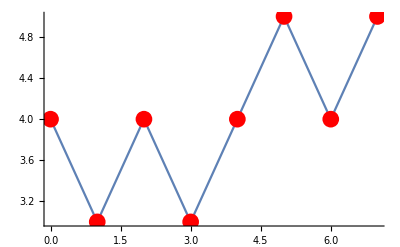
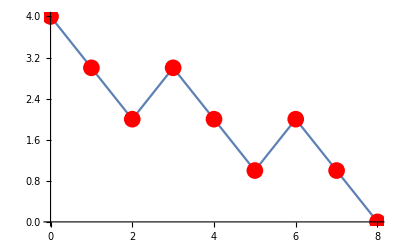
Result for randomWalk:  | {0,10,4,7} | {{0,4},{1,3},{2,2},{3,1},{4,0},{5,1},{6,0},{7,1}}
Result for plotRandomWalk:  | {0,10,4,7} | -Graphics-
Result for stopRandomWalk:  | {0,10,4} | {-Graphics-,{{0,4},{1,3},{2,2},{3,3},{4,2},{5,1},{6,2},{7,1},{8,0}}}
Result for stopPointRandomWalk:  | {0,10,4} | {13,10}
Result for lowerUpper:  | {0,10,4,7} | {Lower: 6,Upper: 1}
Result for modRandomWalk:  | {0,10,4,0.4,7} | modRandomWalk[0,10,4,0.4,7]
Result for modPlotRandomWalk:  | {0,10,4,0.4,7} | modPlotRandomWalk[0,10,4,0.4,7]
Result for modStopRandomWalk:  | {0,10,0.4,4} | modStopRandomWalk[0,10,0.4,4]
Result for modStopPointRandomWalk:  | {0,10,0.4,4} | modStopPointRandomWalk[0,10,0.4,4]
Result for randomWalk3D:  | {{0,0},{10,15},{7,7},7} | {{0,7,7},{1,6,6},{2,7,7},{3,6,8},{4,7,9},{5,6,10},{6,7,9},{7,6,8}}
Result for plotRandomWalk3D:  | {{0,0},{10,15},{7,7},7} | -Graphics3D-
Result for stopRandomWalk3D:  | {{0,0},{10,15},{7,7}} | {-Graphics3D-,{{0,7,7},{1,6,8},{2,7,9},{3,6,10},{4,7,11},{5,8,10},{6,7,9},{7,6,10},{8,5,9},{9,4,8},{10,3,9},{11,4,8},{12,3,9},{13,2,8},{14,3,9},{15,2,8},{16,3,7},{17,2,8},{18,1,9},{19,2,8},{20,1,9},{21,2,8},{22,1,7},{23,0,6}}}
Result for stopPointRandomWalk3D:  | {{0,0},{10,15},{7,7}} | {5,10,8}
Result for lowerUpper3D:  | {{0,0},{10,15},{7,7},7} | {0,7,0,0,0}

```mathematica
(* testing each function - name and simple execution *)
Module[
{i},
Grid[
Table[testFunctionExists[funNameLstRandomWalk[[i]], formalParamlstRandomWalk[[i]], actualParamlstRandomWalk[[i]]],
 {i, 1,  Length[funNameLstRandomWalk]}
],
Frame->All
]
]
```

#### testing return type of all functions

execute this cell

```mathematica
correctTypeLstRandomWalk = { 
{List, {"individual",{ {1,2}, {1,2}, {1,2}}}},  
{Graphics, {}},
{List, {"individual", {Graphics[Point[{2,1}]], {1,2,3}}}}, 
{List, {"individual", {1,2}}},  
{List,{"individual", {1,2}}}, 

{List, {"individual",{ {1,2}, {1,2}, {1,2}}}},  
{Graphics, {}},
{List, {"individual", {Graphics[Point[{2,1}]], {1,2,3}}}}, 
{List, {"individual", {1,2}}},

{List, {"individual",{ {1,2}, {1,2}, {1,2}}}},  
{Graphics3D,{}},
{List, {"individual", {Graphics3D[Point[{2,1,0}]], {1,2,3}}}}, 
{List, {"individual", {1,2,3}}},  
{List,{"individual", {1,2,3,4,5}}}
};
```

```mathematica
Module[{testResult,i},
TableForm[Table[
Print["processing: " ,funNameLstRandomWalk[[i]]]; testResult=Apply[ToExpression[funNameLstRandomWalk[[i]]], actualParamlstRandomWalk[[i]]];
{funNameLstRandomWalk[[i]],verifyReturnTypeAndStructure[testResult,  correctTypeLstRandomWalk[[i]]]},
 {i, 1, Length[funNameLstRandomWalk]}
]
]
]
```

processing: randomWalk

Correct types

processing: plotRandomWalk

Correct types

processing: stopRandomWalk

Correct types

processing: stopPointRandomWalk

Correct types

processing: lowerUpper

Correct types

processing: modRandomWalk

Error - incorrect type returned; should be a List

processing: modPlotRandomWalk

Error - incorrect type returned; should be a Graphics

processing: modStopRandomWalk

Error - incorrect type returned; should be a List

processing: modStopPointRandomWalk

Correct types

processing: randomWalk3D

Correct types

processing: plotRandomWalk3D

Correct types

processing: stopRandomWalk3D

Correct types

processing: stopPointRandomWalk3D

Correct types

processing: lowerUpper3D

{{21,10,2},{3,10,8},{3,10,6},{28,3,15},{10,5,15},{5,10,12},{7,10,6}}

Correct types

randomWalk | True
plotRandomWalk | True
stopRandomWalk | True
stopPointRandomWalk | True
lowerUpper | True
modRandomWalk | False
modPlotRandomWalk | False
modStopRandomWalk | False
modStopPointRandomWalk | True
randomWalk3D | True
plotRandomWalk3D | True
stopRandomWalk3D | True
stopPointRandomWalk3D | True
lowerUpper3D | True

```mathematica
modrandomWalk[0, 10, 10, 0, 8]
```

{{0,10},{1,9},{2,8},{3,7},{4,8},{5,9},{6,10},{7,9},{8,8}}

### RandomWalk problem - individual functions

#### Code testing functions - RandomWalk -- execute cell AFTER basic testing for Random Walks

```mathematica
testRandomWalk3D[testCases_]:=Module [
{low, upp, start, length,res,checkRes},
Grid[
Table[
SeedRandom[201];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
length=item[[4]];
res = Check[ 
TimeConstrained[ randomWalk3D[ low,upp,start,length], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={randomWalk, {low, upp, start, length}, res},
(* else *)
	   checkRes={randomWalk,  {low, upp, start, length}, checkRandomWalk3DResult[res, {length+1,low,upp}]}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testStopPointRandomWalk3D[testCases_]:=Module [
{low, upp, start, res,checkRes},
Grid[
Table[
SeedRandom[213];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
res = Check[ 
TimeConstrained[ stopRandomWalk3D[low,upp,start], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={stopRandomWalk3D,{low, upp, start}, res},
(* else *)
SeedRandom[213];	   
 checkRes={{ToString[stopRandomWalk3D]<> "\n" <> ToString[stopPointRandomWalk3D]},{low, upp, start},res[[1]],Last[res[[2]]],stopPointRandomWalk3D[low,upp, start]}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testLowerUpper3D[testCases_]:=Module [
{low, upp, start, repeat, res,checkRes},
Grid[
Table[
SeedRandom[203];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
repeat = item[[4]];
res = Check[ 
TimeConstrained[ lowerUpper3D[low,upp,start, repeat], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={lowerUpper3D,{low, upp, start, repeat}, res},
(* else *)	   
 checkRes={lowerUpper3D,{low, upp, start, repeat},res, Total[res]}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testRandomWalk[testLst_]:=Module [
{low, upp, start, length,res,checkRes},
Grid[
Table[
SeedRandom[201];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
length=item[[4]];
res = Check[ 
TimeConstrained[ randomWalk[low,upp,start,length], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={randomWalk,{low, upp, start, length}, res},
(* else *)
	   checkRes={randomWalk,{low, upp, start, length},   checkRandomWalkResult[res, {length+1,low,upp},0]}
];
checkRes,
{item, testLst}
],
Frame->All
]
]
```

```mathematica
testStopRandomWalStopPointRandomWalk[testCases_]:=Module [
{low, upp, start, res,checkRes},
Grid[
Table[
SeedRandom[203];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
res = Check[ 
TimeConstrained[ stopRandomWalk[low,upp,start], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={stopRandomWalk,{low, upp, start}, res},
(* else *)
SeedRandom[203];	   
 checkRes={{ToString[stopRandomWalk]<> "\n" <> ToString[stopPointRandomWalk]},{low, upp, start},res[[1]],Last[res[[2]]],stopPointRandomWalk[low,upp, start]}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testLowerUpper[testCases_]:=Module [
{low, upp, start, repeat, prob,res,checkRes},
Grid[
Table[
SeedRandom[203];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
repeat = item[[4]];
res = Check[ 
TimeConstrained[ lowerUpper[low,upp,start, repeat], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={lowerUpper,{low, upp, start, repeat}, res},
(* else *)
SeedRandom[203];	   
 checkRes={lowerUpper,{low, upp, start, repeat},res, Total[res] == repeat}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testModRandomWalk[testCases_]:=Module [
{low, upp, start, length, prob,res,checkRes},
Grid[
Table[
SeedRandom[201];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
prob=item[[4]];
length=item[[5]];
res = Check[ 
TimeConstrained[ modRandomWalk[low,upp,start,prob,length], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={modRandomWalk,{low, upp, start, prob,  length}, res},
(* else *)
		(*Print["res = ", res];*)
	   checkRes={modRandomWalk,{low, upp, start,prob, length},   checkRandomWalkResult[res, {length+1,low,upp},prob]}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testModStopStopPointRandomWalk[testCases_]:= Module [
{low, upp, start, res,checkRes},
Grid[
Table[
SeedRandom[203];
low=item[[1]];
upp=item[[2]];
start=item[[3]];
res = Check[ 
TimeConstrained[ stopRandomWalk[low,upp,start], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={stopRandomWalk,{low, upp, start}, res},
(* else *)
SeedRandom[203];	   
 checkRes={stopRandomWalk,{low, upp, start},res[[1]],Last[res[[2]]],stopPointRandomWalk[low,upp, start]}
];
checkRes,
{item, testCases}
],
Frame->All
]
]
```

#### testing return values - for students randomWalk

```mathematica
testRandomWalkCases={{0,10,4,70},{2,3,3,40}, {2,12,7,5000},{2,12,9,5000}};
```

```mathematica
testRandomWalk[testRandomWalkCases]
```

randomWalk | {0,10,4,70} | {0.528571,0.471429}
randomWalk | {2,3,3,40} | {0.5,0.5}
randomWalk | {2,12,7,5000} | {0.5,0.5}
randomWalk | {2,12,9,5000} | {0.4998,0.5002}

#### testing return values - for students stopRandomWalk, stopPointRandomWalk

```mathematica
testStopRandomWalkStopPointRandomWalkCases={{0,10,4},{2,3,3}, {2,12,7},{2,12,9}};
```

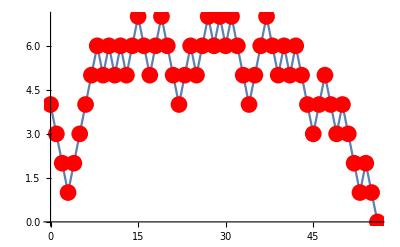
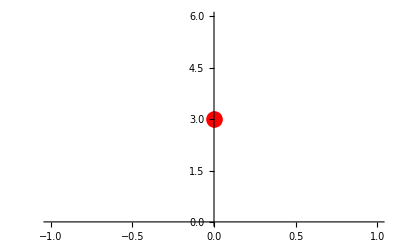
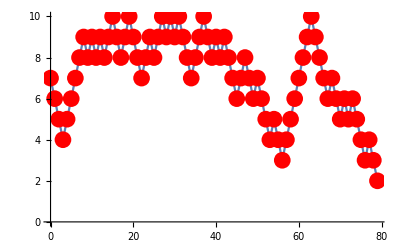
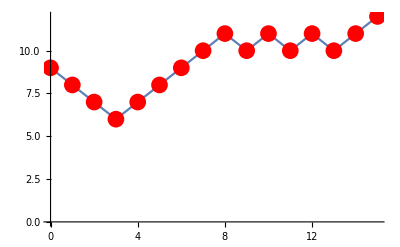
{stopRandomWalk
stopPointRandomWalk} | {0,10,4} | -Graphics- | {56,0} | {57,0}
{stopRandomWalk
stopPointRandomWalk} | {2,3,3} | -Graphics- | {0,3} | {1,3}
{stopRandomWalk
stopPointRandomWalk} | {2,12,7} | -Graphics- | {79,2} | {80,2}
{stopRandomWalk
stopPointRandomWalk} | {2,12,9} | -Graphics- | {15,12} | {16,12}

```mathematica
testStopRandomWalStopPointRandomWalk[testStopRandomWalkStopPointRandomWalkCases]
```

#### testing return values - for students lowerUpper

```mathematica
testLowerUpperCases={{0,10,4, 5000},{2,3, 3,1000}, {2,12,7,5000},{2,12,9, 10000}};
```

```mathematica
testLowerUpper[testLowerUpperCases]
```

lowerUpper | {0,10,4,5000} | {3037,1963} | True
lowerUpper | {2,3,3,1000} | {0,1000} | True
lowerUpper | {2,12,7,5000} | {2549,2451} | True
lowerUpper | {2,12,9,10000} | {3034,6966} | True

#### testing return values - for students modRandomWalk

```mathematica
testModRandomWalkCases={{0,10,4,0, 70},{2,3,3, 0.6,40}, {2,12,7, 0.4,5000},{2,12,9, 0.3,5000}};
```

```mathematica
testModRandomWalk[ testModRandomWalkCases]
```

Incorrect length of result: is 5 instead of 71

Incorrect length of result: is 5 instead of 41

Incorrect length of result: is 5 instead of 5001

Incorrect length of result: is 5 instead of 5001

modRandomWalk | {0,10,4,0,70} | False
modRandomWalk | {2,3,3,0.6,40} | False
modRandomWalk | {2,12,7,0.4,5000} | False
modRandomWalk | {2,12,9,0.3,5000} | False

```mathematica
Length@modrandomWalk[0,10,4,0, 70]
```

71

```mathematica
Length@modrandomWalk[2,3,3, 0.6,40]
```

41

```mathematica
Length@modrandomWalk[2,12,7, 0.4,5000]
```

5001

```mathematica
Length@modrandomWalk[2,12,9, 0.3,5000]
```

5001

#### testing return values - for students modStopRandomWalk, modStopPointRandomWalk

```mathematica
testModStopStopPointRandomWalkCases={{0,10,4},{2,3,3}, {2,12,7},{2,12,9}};
```

```mathematica
testModStopStopPointRandomWalk[ testModStopStopPointRandomWalkCases]
```

stopRandomWalk | {0,10,4} | -Graphics- | {56,0} | {57,0}
stopRandomWalk | {2,3,3} | -Graphics- | {0,3} | {1,3}
stopRandomWalk | {2,12,7} | -Graphics- | {79,2} | {80,2}
stopRandomWalk | {2,12,9} | -Graphics- | {15,12} | {16,12}

#### testing return values - for students modLowerUpper - not part of the assignment

```mathematica
(*testModLowerUpperCases={{0,10,4, 5000},{2,3, 3,1000}, {2,12,7,5000},{2,12,9, 10000}};*)
```

```mathematica
(*testModLowerUpper  [testModLowerUpperCases]*)
```

#### testing return values - for students randomWalk3D

```mathematica
testRandomWalk3DCases={
{{0,0}, {10,15}, {7,7}, 7},
{{1,4}, {3, 8}, {3,8},70},
{{2,9}, {10,21}, {4,17}, 700}

};
```

```mathematica
testRandomWalk3D [testRandomWalk3DCases]
```

randomWalk | {{0,0},{10,15},{7,7},7} | {0.428571,0.571429}
randomWalk | {{1,4},{3,8},{3,8},70} | {0.228571,0.257143,0.257143,0.257143}
randomWalk | {{2,9},{10,21},{4,17},700} | {0.267143,0.237143,0.228571,0.267143}

#### testing return values - for students stopRandomWalk3D, stopPointRandomWalk3D

```mathematica
testStopPointRandomWalk3DCases={
{{0,0}, {10,15}, {7,7}},
{{1,4}, {3, 8}, {2,6}},
{{2,9}, {10,21}, {4,17}}
};
```

```mathematica
testStopPointRandomWalk3D [testStopPointRandomWalk3DCases]
```

{stopRandomWalk3D
stopPointRandomWalk3D} | {{0,0},{10,15},{7,7}} | -Graphics3D- | {7,10,8} | {7,10,8}
{stopRandomWalk3D
stopPointRandomWalk3D} | {{1,4},{3,8},{2,6}} | -Graphics3D- | {1,1,7} | {1,1,7}
{stopRandomWalk3D
stopPointRandomWalk3D} | {{2,9},{10,21},{4,17}} | -Graphics3D- | {18,10,17} | {18,10,17}

#### testing return values - for students lowerUpper3D

```mathematica
testLowerUpper3DCases={
{{0,0}, {10,15}, {7,7}, 700},
{{1,4}, {3, 8}, {2,6},5000},
{{2,9}, {10,21}, {4,17}, 7000}
};
```

```mathematica
testLowerUpper3D [testLowerUpper3DCases];
```

### Wonderword problem - basic testing

#### testing whether all functions exist and can be executed - Wonderword problem

execute cell!!!

```mathematica
funNameLstRaw = {hw3checkStartDirection, hw3checkStart,hw3findWord, hw3findAllWords, hw3checkWonder};
```

```mathematica
formalParamlstRaw={{ hw3letterRect, hw3word, hw3startLoc, hw3direction},{hw3letterRect, hw3word, hw3startLoc},{hw3letterRect,hw3word},{hw3letterRect,hw3wordLst}, {hw3letterRect, hw3wordLst}};
```

```mathematica
funNameLst=Table[StringDrop[ToString[item],3],{item, funNameLstRaw}];
```

```mathematica
Table[ToExpression["Remove["<>ToString[item]<>"]"],{item, funNameLstRaw}];
```

```mathematica
formalParamlst=
Table [
	Table [ToString[item],{item, blah}],
	{blah, formalParamlstRaw}
];
```

```mathematica
hw3Test1={{"b","b","b","b","b","b"},{"v","v","t","v","v","v"},{"k","k","k","o","k","k"},{"i","i","i","i","w","i"},{"0","0","0","0","0","0"}};
display = Grid[hw3Test1, Frame->All]
```

b | b | b | b | b | b
v | v | t | v | v | v
k | k | k | o | k | k
i | i | i | i | w | i
0 | 0 | 0 | 0 | 0 | 0

```mathematica
actualParamlst = { {hw3Test1, "tow", {2,3}, {1,1}},  {hw3Test1, "tow", {2,3}},   {hw3Test1, "tow"}, {hw3Test1, {"tow"}}, {hw3Test1, {"tow"}}};
```

```mathematica
Module[
{i},Grid[
Table[testFunctionExists[funNameLst[[i]], formalParamlst[[i]], actualParamlst[[i]]],
 {i, 1,Length[funNameLst]}
],
Frame->All
]
]
```

function checkStartDirection exists and is used

function checkStart exists and is used

function findWord exists and is used

function findAllWords exists and is used

function checkWonder exists and is used

Result for checkStartDirection:  | {{{b,b,b,b,b,b},{v,v,t,v,v,v},{k,k,k,o,k,k},{i,i,i,i,w,i},{0,0,0,0,0,0}},tow,{2,3},{1,1}} | True
Result for checkStart:  | {{{b,b,b,b,b,b},{v,v,t,v,v,v},{k,k,k,o,k,k},{i,i,i,i,w,i},{0,0,0,0,0,0}},tow,{2,3}} | {{1,1}}
Result for findWord:  | {{{b,b,b,b,b,b},{v,v,t,v,v,v},{k,k,k,o,k,k},{i,i,i,i,w,i},{0,0,0,0,0,0}},tow} | {{{2,3},{{1,1}}}}
Result for findAllWords:  | {{{b,b,b,b,b,b},{v,v,t,v,v,v},{k,k,k,o,k,k},{i,i,i,i,w,i},{0,0,0,0,0,0}},{tow}} | {{tow,{{{2,3},{{1,1}}}}}}
Result for checkWonder:  | {{{b,b,b,b,b,b},{v,v,t,v,v,v},{k,k,k,o,k,k},{i,i,i,i,w,i},{0,0,0,0,0,0}},{tow}} | {{tow},{},{}}

#### testing return type of all functions

```mathematica
correctTypeLst = { {Symbol, {}},  
{List, {"individual", {{2,3}}}}, 
{List, {"individual", {{{2,3}, {{2,3}}}}}},  
{List,{"individual", {{ "word", {{{2,3},{{2,3}}}}}}}}, 
{List, {"individual", {{"word", "word"}, { }, { }}}}};
```

```mathematica
Module[{testResult,i},
TableForm[Table[
Print["processing: ", funNameLst[[i]]];
 testResult=Apply[ToExpression[funNameLst[[i]]], actualParamlst[[i]]];
{funNameLst[[i]],verifyReturnTypeAndStructure[testResult,  correctTypeLst[[i]]]},
 {i, 1, Length[funNameLst]}
]
]
]
```

processing: checkStartDirection

Correct types

processing: checkStart

Correct types

processing: findWord

Correct types

processing: findAllWords

Correct types

processing: checkWonder

Correct types

checkStartDirection | True
checkStart | True
findWord | True
findAllWords | True
checkWonder | True

### Wonderword problem - individual functions

#### Code testing functions - Wonder word - -- execute cell AFTER basic testing for WonderWord

```mathematica
testCheckStartDirection[testValueLst_]:= Module[
{rect, word, start, direction, correctRes, res,checkRes, item},
Grid[
Table[
SeedRandom[201];
rect=item[[1]];
word=item[[2]];
start=item[[3]];
direction=item[[4]];
correctRes= item[[5]];
res = Check[ 
TimeConstrained[ checkStartDirection[rect,word,start,direction], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={checkStartDirection,{"rect", word, start, direction}, res},
(* else *)
	   checkRes={checkStartDirection,{"rect", word, start, direction},  res, SameQ[res,correctRes] }
];
checkRes,
{item, testValueLst}
],
Frame->All
]
]
```

```mathematica
testCheckStart[testValueLst_]:= Module[
{rect, word, start, direction, correctRes, res,checkRes, item},
Grid[
Table[
SeedRandom[201];
rect=item[[1]];
word=item[[2]];
start=item[[3]];
correctRes=item[[4]];
res = Check[ 
TimeConstrained[ checkStart[rect,word,start], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={checkStart,{"rect", word, start}, res},
(* else *)
	   checkRes={checkStart,{"rect", word, start},  res, SameQ[res,correctRes] }
];
checkRes,
{item, testValueLst}
],
Frame->All
]
]
```

```mathematica
testfindWord[testValueLst_]:= Module[
{rect, word, start, direction, correctRes, res,checkRes, item},
Grid[
Table[
SeedRandom[201];
rect=item[[1]];
word=item[[2]];
correctRes=item[[3]];
res = Check[ 
TimeConstrained[ findWord[rect,word], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={findWord,{"rect", word}, res},
(* else *)
	   checkRes={findWord,{"rect", word},  res, SameQ[Sort[res],Sort[correctRes]] }
];
checkRes,
{item, testValueLst}
],
Frame->All
]
]
```

```mathematica
testfindAllWords[testValueLst_]:= Module[
{rect, wordLst, start, direction, correctRes, res,checkRes, item},
Grid[
Table[
SeedRandom[201];
rect=item[[1]];
wordLst=item[[2]];
correctRes=item[[3]];
res = Check[ 
TimeConstrained[ findAllWords[rect,wordLst], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={findAllWords,{"rect", wordLst}, res},
(* else *)
	   checkRes={findAllWords,{"rect", wordLst},  res, 
	SameQ[Sort[Table[Sort[item],{item,res}]],Sort[Table[Sort[item],{item,correctRes}]]]}
];
checkRes,
{item, testValueLst}
],
Frame->All
]
]
```

```mathematica
testcheckWonder[testValueLst_]:= Module[
{rect, wordLst, start, direction, correctRes,res, checkRes, item},
Grid[
Table[
rect=item[[1]];
wordLst=item[[2]];
correctRes=item[[3]];
res = Check[ 
TimeConstrained[ checkWonder[rect,wordLst], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={checkWonder,{"rect", wordLst}, res},
(* else *)
	   checkRes={checkWonder,{"rect", wordLst},  res, 
		SameQ[Table[Sort[item],{item,res}],Table[Sort[item],{item,correctRes}]]}
];
checkRes,
{item, testValueLst}
],
Frame->All
]
]
```

#### code create the two test rectangles -- execute before testing remaining cells

```mathematica
rectangleHW={{"b","r","e","a","d"},{"m","o","u","s","e"},{"s","t","o","v","e"},{"f","l","o","w","r"},{"g","r","a","p","e"}};
display = Grid[rectangleHW, Frame->All]
```

b | r | e | a | d
m | o | u | s | e
s | t | o | v | e
f | l | o | w | r
g | r | a | p | e

```mathematica
rect2={{"t","p", "e"},{"o","e", "c"},{"t","n", "a"},{"n","o", "r"}}
Grid[rect2, Frame->All]
```

{{t,p,e},{o,e,c},{t,n,a},{n,o,r}}

t | p | e
o | e | c
t | n | a
n | o | r

#### testing return values - for checkStartDirection

```mathematica
testStartDirectionCases={{rectangleHW,"read", {1,2}, {0,1}, True},{rectangleHW,"read", {1,3}, {0,1}, False},{rectangleHW,"bead", {1,2}, {0,1}, False}, {rect2, "tea", {1,1}, {1,1}, True}, {rect2, "tee" ,{3,1},{-1,1}, True}, {rect2, "race" ,{4,3},{-1, 0}, True},{rect2, "race" ,{1,3},{1, 0}, False}};
```

```mathematica
rectangleHW
```

{{b,r,e,a,d},{m,o,u,s,e},{s,t,o,v,e},{f,l,o,w,r},{g,r,a,p,e}}

```mathematica
testCheckStartDirection[testStartDirectionCases]
```

checkStartDirection | {rect,read,{1,2},{0,1}} | True | True
checkStartDirection | {rect,read,{1,3},{0,1}} | False | True
checkStartDirection | {rect,bead,{1,2},{0,1}} | False | True
checkStartDirection | {rect,tea,{1,1},{1,1}} | True | True
checkStartDirection | {rect,tee,{3,1},{-1,1}} | True | True
checkStartDirection | {rect,race,{4,3},{-1,0}} | True | True
checkStartDirection | {rect,race,{1,3},{1,0}} | False | True

#### testing return values - for checkStart

```mathematica
testStartCases={{rectangleHW,"CPS", {4,5}, {}},{rectangleHW,"re", {4,5}, {{-1,0},{1,0}}},{rectangleHW,"pot", {5,4},{ {-1,-1}}},{rect2, "tea", {1,1}, {{1,1}}}, {rect2, "tee" ,{3,1},{{-1,1}}}, {rect2, "race" ,{4,3},{{-1, 0}}},{rect2, "race" ,{1,3},{}}};
```

```mathematica
testCheckStart[testStartCases]
```

checkStart | {rect,CPS,{4,5}} | {} | True
checkStart | {rect,re,{4,5}} | {{-1,0},{1,0}} | True
checkStart | {rect,pot,{5,4}} | {{-1,-1}} | True
checkStart | {rect,tea,{1,1}} | {{1,1}} | True
checkStart | {rect,tee,{3,1}} | {{-1,1}} | True
checkStart | {rect,race,{4,3}} | {{-1,0}} | True
checkStart | {rect,race,{1,3}} | {} | True

#### testing return values - for findWord

```mathematica
testfindWordCases={{rectangleHW,"CPS", {}},{rectangleHW,"re", {{{4,5} ,{{-1,0},{1,0}}},{{1,2},{{0,1}}}}},{rectangleHW,"pot", {{{5,4},{ {-1,-1}}}}},{rect2, "tea", {{{1,1}, {{1,1}}}}}, {rect2, "tee" ,{{{3,1},{{-1,1}}}}}, {rect2, "race" ,{{{4,3},{{-1, 0}}}}},{rect2, "rage" ,{}}};
```

```mathematica
testfindWord[testfindWordCases]
```

findWord | {rect,CPS} | {} | True
findWord | {rect,re} | {{{1,2},{{0,1}}},{{4,5},{{-1,0},{1,0}}}} | True
findWord | {rect,pot} | {{{5,4},{{-1,-1}}}} | True
findWord | {rect,tea} | {{{1,1},{{1,1}}}} | True
findWord | {rect,tee} | {{{3,1},{{-1,1}}}} | True
findWord | {rect,race} | {{{4,3},{{-1,0}}}} | True
findWord | {rect,rage} | {} | True

#### testing return values - for findAllWords

```mathematica
testfindAllWordCases={
{rectangleHW,wordlst, {{"read",{{{1,2},{{0,1}}}}},{"top",{{{3,2},{{1,1}}}}},{"pot",{{{5,4},{{-1,-1}}}}},{"wolf",{{{4,4},{{0,-1}}}}},{"deer",{{{1,5},{{1,0}}}}},{"sol",{{{2,4},{{1,-1}}}}},{"rove",{{{5,2},{{-1,1}}}}},{"reed",{{{4,5},{{-1,0}}}}}}},
{rectangleHW,wordlst2,{{"read",{{{1,2},{{0,1}}}}},{"top",{{{3,2},{{1,1}}}}},{"re","multiple matches"},{"pot",{{{5,4},{{-1,-1}}}}},{"wolf",{{{4,4},{{0,-1}}}}},{"deer",{{{1,5},{{1,0}}}}},{"sol",{{{2,4},{{1,-1}}}}},{"rove",{{{5,2},{{-1,1}}}}},{"to","multiple matches"},{"reed",{{{4,5},{{-1,0}}}}}}},
{rect2, wordlst21, {{"ant",{{{3,3},{{0,-1}}}}},{"pen",{{{1,2},{{1,0}}}}},{"tea",{{{1,1},{{1,1}}}}},{"race",{{{4,3},{{-1,0}}}}},{"nor",{{{4,1},{{0,1}}}}},{"one",{{{4,2},{{-1,0}}}}},{"tee",{{{3,1},{{-1,1}}}}}}},
{rect2, wordlst2, {{"to","multiple matches"}}}
};
wordlst={"kjhg","pan", "read", "top", "jhg","pot", "wolf", "deer", "sol", "rove", "reed","hg"};
wordlst2={"kjhg","pan", "read", "top","re", "jhg","pot", "wolf", "deer", "sol", "rove","to", "reed","hg"};
wordlst21={"ant", "pen", "tea", "tear", "race","nor", "not", "one", "tee"};
```

```mathematica
testfindAllWords[testfindAllWordCases]
```

findAllWords | {rect,{kjhg,pan,read,top,jhg,pot,wolf,deer,sol,rove,reed,hg}} | {{read,{{{1,2},{{0,1}}}}},{top,{{{3,2},{{1,1}}}}},{pot,{{{5,4},{{-1,-1}}}}},{wolf,{{{4,4},{{0,-1}}}}},{deer,{{{1,5},{{1,0}}}}},{sol,{{{2,4},{{1,-1}}}}},{rove,{{{5,2},{{-1,1}}}}},{reed,{{{4,5},{{-1,0}}}}}} | True
findAllWords | {rect,{kjhg,pan,read,top,re,jhg,pot,wolf,deer,sol,rove,to,reed,hg}} | {{read,{{{1,2},{{0,1}}}}},{top,{{{3,2},{{1,1}}}}},{re,multiple matches},{pot,{{{5,4},{{-1,-1}}}}},{wolf,{{{4,4},{{0,-1}}}}},{deer,{{{1,5},{{1,0}}}}},{sol,{{{2,4},{{1,-1}}}}},{rove,{{{5,2},{{-1,1}}}}},{to,multiple matches},{reed,{{{4,5},{{-1,0}}}}}} | True
findAllWords | {rect,{ant,pen,tea,tear,race,nor,not,one,tee}} | {{ant,{{{3,3},{{0,-1}}}}},{pen,{{{1,2},{{1,0}}}}},{tea,{{{1,1},{{1,1}}}}},{race,{{{4,3},{{-1,0}}}}},{nor,{{{4,1},{{0,1}}}}},{one,{{{4,2},{{-1,0}}}}},{tee,{{{3,1},{{-1,1}}}}}} | True
findAllWords | {rect,{kjhg,pan,read,top,re,jhg,pot,wolf,deer,sol,rove,to,reed,hg}} | {{to,multiple matches}} | True

#### testing return values - for checkWonder

```mathematica
testcheckWonderCases={
{rectangleHW,wordlst3,{{"read","top","pot","wolf","deer","sol","rove","reed"},{},{}}},
{rectangleHW,wordlst2,{{"read","top","pot","wolf","deer","sol","rove","reed"},{"re","to"},{"hg","jhg","kjhg","pan"}}},
{rect2, wordlst21, {{"ant", "pen", "tea",  "race","nor",  "one", "tee"}, {}, {"tear","not"}}},
{rect2, wordlst22, {{"race"},{"to"},{"rage","re"}}}
};
wordlst3={"read", "top","pot", "wolf", "deer", "sol", "rove", "reed"};
     wordlst2={"kjhg","pan", "read", "top","re", "jhg","pot", "wolf", "deer", "sol", "rove","to", "reed","hg"};
wordlst21={"ant", "pen", "tea", "tear", "race","nor", "not", "one", "tee"};
wordlst22={"re", "race", "to", "rage"};
```

```mathematica
testcheckWonder[testcheckWonderCases]
```

checkWonder | {rect,{read,top,pot,wolf,deer,sol,rove,reed}} | {{read,top,pot,wolf,deer,sol,rove,reed},{},{}} | True
checkWonder | {rect,{kjhg,pan,read,top,re,jhg,pot,wolf,deer,sol,rove,to,reed,hg}} | {{read,top,pot,wolf,deer,sol,rove,reed},{re,to},{kjhg,pan,jhg,hg}} | True
checkWonder | {rect,{ant,pen,tea,tear,race,nor,not,one,tee}} | {{ant,pen,tea,race,nor,one,tee},{},{tear,not}} | True
checkWonder | {rect,{re,race,to,rage}} | {{race},{to},{re,rage}} | True